# DataRegion package

## by Ian Hinder

## Initialisation

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ian/Projects/sfg

```mathematica
<<"DataRegion.m"
```

## Documentation

The "DataRegion" Mathematica package provides a simple representation of a 3D block of numbers on a uniform Cartesian coordinate grid. The package uses an abstract type called "DataRegion" to represent each block.

A DataRegion object is printed in Mathematica as DataRegion[varName, dims, dataRange] to avoid printing large quantities of data.  To see the full structure, including all the data, use FullForm.

### ReadCarpetHDF5Variable[file, var, it, rl]

This function opens a set of Carpet HDF5 files and loads variable var, iteration it, refinement level rl, from the file set and returns it as a single DataRegion object.  This function will not work properly (or at all) with multipatch data.  It is currently assumed that the filename given, file, ends in the suffix ".file_0.h5" and that there is a corresponding set of files ".file_<c>.h5".  This set of files is opened, and component c is read from each one.  The outermost cctk_nghostzones points are stripped from each component, and the components are then merged into a single DataRegion object.  If the components are disconnected, a single enclosing cuboid grid is created, and points which are not on any of the components are initialised to None.  In future, we could detect disconnected components and return a list of DataRegion objects for each one.

### ReadVTKFile[file]

Read the data file from file in VTK format and return it as a DataRegion object. file can either be a string, for a filename, or a stream object.  Currently there is very little error-checking, and strong assumptions are made about the format of the data.  It must be single-precision and in binary, not ascii, format.

### GetData[v]

Return a nested list, of depth 3 containing the values from the DataRegion object v.  The data is ordered in column-major order (the same as Carpet), so when accessing points from the list, the array ordering is data[[iz,iy,ix]].  This means that extracting a slice of constant z-coordinate is simple: data[[iz]].

### GetOrigin[v]

Return a list {ox, oy, oz} containing the minimum x, y and z coordinates of the block.

### GetSpacing[v]

Return a list {dx, dy, dz} containing the spacing between points in the x, y and z directions.

### GetDimensions[v]

Return a list {nx, ny, nz} containing the number of points in the x, y and z directions.

### GetDataRange[v]

Return a list of the form {{xmin, xmax}, {ymin, ymax}, {zmin, zmax}} describing the minimum and maximum coordinates of the block.  This list can be used in the DataRange option of various Mathematica plotting functions.

### GetVariableName[v]

Return a string containing the variable name of the DataRegion v as recorded in the original file.

### Interpolation[v, ...]

The Interpolation function has been overloaded to work on DataRegion objects.  Internally, it uses ListInterpolation with the data and data ranges.  You can supply additional options for ListInterpolation to this function.  The resulting function will generically be a function of three variables, but in the case where nz = 1, it will be a function of two variables.  This is necessary because ListInterpolation cannot perform the interpolation if one of the dimensions of the list is too small to interpolate at the requested order.  This could be confusing, so in future a workaround will be added here so that all results of Interpolation[v] are functions of three variables.  Interpolation might not work if the DataRegion contains data with value None, as will happen with Carpet data with disconnected components.

### SliceData[v, dim:3, coord:0]

Return a DataRegion object which is a slice through v in a plane perpendicular to dimension dim (from 1 to 3).  Currently only dim=3 is supported.  coord is the coordinate value at which to take the slice.  Since DataRegions are always 3 dimensional, the resulting DataRegion object will have one of its dimensions set to 1.  To obtain the numerical data, use GetData on the resulting object.  For convenience, dim and coord arguments can be omitted, defaulting to 3 and 0.0 respectively.

### DataRegionDensityPlot[v,...]

This is a wrapper for the Mathematica DensityPlot function.  It operates on sliced (i.e. with nz = 1) DataRegion objects, automatically converting the object to a list and setting the data ranges appropriately.  You can use any DensityPlot arguments with this function.

### DataRegionArrayPlot[v,...]

This is a wrapper for the Mathematica ArrayPlot function.  It operates on sliced (i.e. with nz = 1) DataRegion objects, automatically converting the object to a list and setting the data ranges appropriately.  You can use any ArrayPlot arguments with this function.

### QuickSlicePlot[v, {min, max}, colorMap,...]

This provides a quick way to plot a DataRegion object slice.  It displays coordinates as well as a colormap key.  min and max correspond to the minimum and maximum values in the data to assign to 0 and 1 in the color map.  colorMap defaults to "TemperatureMap"; use ColorData["Gradients"] to get the list of possible color maps.

## Notes

Currently, only slices in the z-direction are supported.  This can be easily fixed by switching to using Part in the SliceData function

Interpolation on a DataRegion object with one of the dimensions small needs to be fixed.

We can probably support DataRegion objects with arbitrary numbers of dimensions relatively simply, and this would remove the slight problem with slicing.

## DataRegion Example

```mathematica
gxx=ReadCarpetHDF5Variable["sch_3c/output-0000/sch_3c/admbase::metric.file_0.h5","ADMBASE::gxx",0,0]
```

DataRegion[ADMBASE::gxx, {47, 47, 47}, {{-2.875, 2.875}, {-2.875, 2.875}, {-2.875, 2.875}}

```mathematica
gxxSlice=SliceData[gxx]
```

DataRegion[ADMBASE::gxx, {47, 47, 1}, {{-2.875, 2.875}, {-2.875, 2.875}, {0, 0}}

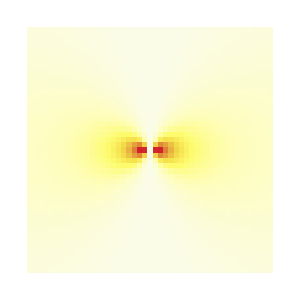

```mathematica
QuickSlicePlot[gxxSlice,{-1,1}]
```

(Note that the Cartesian components of g are not spherically symmetric.)

```mathematica
GetOrigin[gxx]
```

{-2.875,-2.875,-2.875}

```mathematica
GetSpacing[gxx]
```

{0.125,0.125,0.125}

```mathematica
GetDimensions[gxx]
```

{47,47,47}

```mathematica
{{xMin,xMax},{yMin,yMax},{zMin,zMax}}=GetDataRange[gxx]
```

{{-2.875,2.875},{-2.875,2.875},{-2.875,2.875}}

```mathematica
GetVariableName[gxx]
```

ADMBASE::gxx

```mathematica
gxxFn=Interpolation[gxx]
```

InterpolatingFunction[{{-2.875,2.875},{-2.875,2.875},{-2.875,2.875}},<>]

```mathematica
gxxFn[1.0,1.5,2.0]
```

1.10245

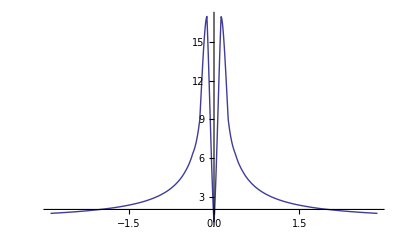

```mathematica
Plot[gxxFn[x,0,0],{x,xMin,xMax},PlotRange->All]
```

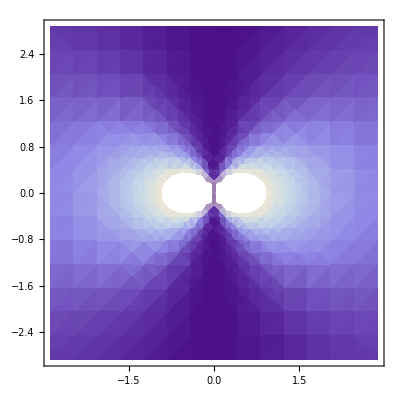

```mathematica
DensityPlot[gxxFn[x,y,0],{x,xMin,xMax},{y,yMin,yMax}]
```